Two-Qubit Gates

Controlled-NOT Gate (CNOT)paclet:Q3/tutorial/TwoQubitGates#1585062394 | Controlled-Unitary Gatespaclet:Q3/tutorial/TwoQubitGates#1455445268
Controlled-Z Gate (CZ)paclet:Q3/tutorial/TwoQubitGates#29167796 | General Unitary Gatespaclet:Q3/tutorial/TwoQubitGates#1476129218
SWAP Gatepaclet:Q3/tutorial/TwoQubitGates#1218939314 |

See also Section 2.2 of the Quantum Workbook (Springer, 2022)https://doi.org/10.1007/978-3-030-91214-7.

This document introduces quantum logic gate operations acting on two qubits. Such operations are represented by 4×4 unitary matrices. We will see that any two-qubit gate operations can be decomposed into controlled-unitary gates. A controlled-unitary gate acts a unitary operator on one qubit depending on the logical state of the other qubit. A controlled-unitary gate on two qubits can be further decomposed into factors including only the CNOT gate and single-qubit rotation gates. In this sense, the CNOT gate alone is sufficient for any two-qubit gate.

The controlled-unitary and CNOT gates have various interesting properties that make them useful in implementing quantum algorithms. In this document, we first examine the basic properties of the CNOT gate, and in particular, how it is used to generate an entanglement between two qubits. Then, we discuss the properties of the controlled-unitary gate and describe how to implement a controlled-unitary gate in terms of the CNOT gate and single-qubit rotations. Finally, we discuss how an arbitrary two-qubit unitary operation can be decomposed into controlled-unitary gates.

CNOTpaclet:Q3/ref/CNOTQ3 Package Symbol | The controlled-NOT or CNOT gate
CZpaclet:Q3/ref/CZQ3 Package Symbol | The controlled-Z or CZ gate
SWAPpaclet:Q3/ref/SWAPQ3 Package Symbol | The SWAP gate exchanging the states between two qubits
ControlledUpaclet:Q3/ref/ControlledUQ3 Package Symbol | Controlled-unitary gates
TwoLevelUpaclet:Q3/ref/TwoLevelUQ3 Package Symbol | Represents two-level unitary transformation
GrayTwoLevelUpaclet:Q3/ref/GrayTwoLevelUQ3 Package Symbol | Rewrite a two-level unitary transformation in terms of the controlled-unitary and CNOT gates

Two-qubit gates available in Q3.

Make sure that the Q3 package is loaded to use the demonstrations in this documentation.

```mathematica
<<Q3`
```

Throughout this documentation, symbol S will be used to denote qubits and Pauli operators on them. Similarly, symbol c will be used to denote complex-valued coefficients.

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

Controlled-NOT Gate (CNOT)

The  controlled-NOT or CNOTpaclet:Q3/ref/CNOTQ3 Package Symbol gate is a quantum logic gate on two qubits that maps the logical basis states as

CNOT:c⊗t↦c⊗c⊕t

for c,t∈{0,1}, where the first qubit is typically called the control qubit (c) and the second qubit the target qubit (t).

```mathematica
op=CNOT[S[1],S[2]]
```

CNOT[{S_1},{S_2}]

```mathematica
in=Basis[S@{1,2}];
out=op**in;
Thread[in->out]//LogicalForm//TableForm
```

0_S_10_S_2→0_S_10_S_2
0_S_11_S_2→0_S_11_S_2
1_S_10_S_2→1_S_11_S_2
1_S_11_S_2→1_S_10_S_2

It has the following matrix representation in the logical basis

```mathematica
mat=Matrix[op];
MatrixForm[mat]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

and is expressed in terms of the Pauli operators on the control and target qubit as

```mathematica
Elaborate[op]
```

1/2-1/2 S_1^z S_2^x+S_1^z/2+S_2^x/2

```mathematica
Elaborate[op]//PauliForm
```

(I⊗I)/2+(I⊗X)/2+(Z⊗I)/2-(Z⊗X)/2

In quantum circuit model, it is represented as the following circuit element

```mathematica
qc=QuantumCircuit[op]
```

-Graphics-

where the smaller filled circle indicates the dependence on the state of the control qubit and the circled-plus sign denotes the conditional NOT action on the target qubit.

A simple yet important feature of CNOTpaclet:Q3/ref/CNOTQ3 Package Symbol is to copy the logical state of the control qubit to the target bit provided that the target bit is initially set to |0⟩; or the reversed state when the target qubit is in |1⟩. A vital implication is that CNOT generates an entangled state when the control qubit is in a superposition:

```mathematica
in=Ket[]c[0]+Ket[S[1]->1]c[1];
out=op**in;
in->out//LogicalForm//KetFactor//LogicalForm
```

(c_0 0_S_1+c_1 1_S_1)⊗0_S_2→c_0 0_S_10_S_2+c_1 1_S_11_S_2

Applying a single qubit rotation such the Hadamard gate on the control qubit prior to CNOT, one can thus generate entangled states from logical states. In this sense, such a circuit is called a quantum entangler circuit.  In general, the different product states in the logical basis are transformed to different Bell states.

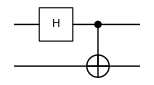

```mathematica
qc=QuantumCircuit[S[1,6],op]
```

```mathematica
in=Basis[S@{1,2}];
out=qc**in;
Thread[in->out]//LogicalForm//TableForm
```

0_S_10_S_2→(0_S_10_S_2)/(√2)+(1_S_11_S_2)/(√2)
0_S_11_S_2→(0_S_11_S_2)/(√2)+(1_S_10_S_2)/(√2)
1_S_10_S_2→(0_S_10_S_2)/(√2)-(1_S_11_S_2)/(√2)
1_S_11_S_2→(0_S_11_S_2)/(√2)-(1_S_10_S_2)/(√2)

One can further generalize the above procedure to generate maximally entangled states between larger systems: Consider two quantum registers, each consisting of n qubits. We respectively call them the ‘control’ and ‘target’ register for the reason that will be clear below. Upon applying the CNOTpaclet:Q3/ref/CNOTQ3 Package Symbol gate on each pair of the corresponding qubits in the two registers as in the quantum circuit,

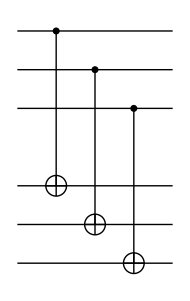

```mathematica
$n=3;
cc=Range[$n];
tt=Range[$n+1,2$n];
qc=QuantumCircuit[Sequence@@Thread[CNOT[S@cc,S@tt]],
"Invisible"->S[$n+1/2]]
```

the logical basis states are transformed as

c⊗t↦c⊗c⊕t .

The above association rule is formally the same as the one in (2.29) for a single pair of qubits. Here, however, c := c_1⊗c_2⊗⋯⊗c_n and t := t_1⊗t_2⊗⋯⊗t_n, and c ⊕ t denotes the bit-wise exclusive OR (or XOR),

c⊕t:=(c_1⊕t_1,c_2⊕t_2,…,c_n⊕t_n) ,

for the n-bit strings c ≡ (c_1,c_2,...,c_n) and t ≡ (t_1,t_2,...,t_n). When the target register is prepared in the state 0≡0^(⊗n), the logical basis state of the control register is copied to the target register,

x⊗0↦x⊗x

under the set of CNOT gates on paired qubits. More interestingly, when the control register is prepared in a superposition, say, 2^(-n/2)∑_(x=0)^(2^n-1) x, and the target register x=0 is in the state 0≡0^(⊗n), the CNOT gate makes a copy of each logical state of the control register to the target register, leading to a maximally entangled state,

(1/2^(n/2)∑_(x=0)^(2^n-1) x)⊗0↦Φ:=1/2^(n/2)∑_(x=0)^(2^n-1) x⊗x

between the two registers (rather than single qubits). Since the superposition 2^(-n/2)∑_(x=0)^(2^n-1) x is obtained just by the Hadamard gates, the maximally entangled state Φ can be generated from the logical state 0⊗0 through the following quantum circuit.

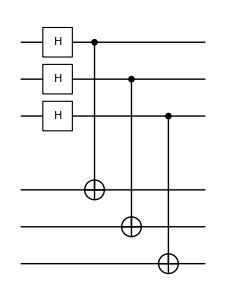

```mathematica
qce=QuantumCircuit[S[cc,6],qc]
```

```mathematica
out=qce**Ket[];
SimpleForm[out,{S@cc,S@tt}]
```

(000;000)/(2 √2)+(001;001)/(2 √2)+(010;010)/(2 √2)+(011;011)/(2 √2)+(100;100)/(2 √2)+(101;101)/(2 √2)+(110;110)/(2 √2)+(111;111)/(2 √2)

It is also interesting to note that even though |Φ⟩ is a maximally entangled state between the control and target registers, it is a product state of n maximally entangled pairs

1/2^(n/2)∑_(x=0)^(2^n-1) x⊗x=⊗_(k=1)^n((0_k⊗0_(n+k)+1_k⊗1_(n+k))/(√2)) .

The entanglement strongly depends on how you partition the system.

Another generalization of copying logical basis states to a series of qubits by consecutively applying CNOT gates with a single control qubit on multiple target qubits is shown in the following quantum circuit,

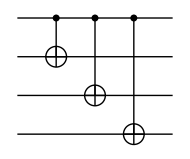

```mathematica
$n=4;
cc={1};
tt=Range[2,$n];
cnot=Distribute[CNOT[S@cc,S@tt],List];
qc=QuantumCircuit[Sequence@@cnot]
```

or equivalently,

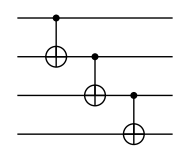

```mathematica
cc=Range[$n-1];
tt=Range[2,$n];
cnot=Thread[CNOT[S@cc,S@tt]];
qc=QuantumCircuit[Sequence@@cnot]
```

When the target qubits are all prepared in the logical basis state |0⟩, the series of CNOT gates makes the transformation

x⊗0⊗⋯⊗0↦x⊗x⊗⋯⊗x

for x=0,1. Therefore, a simple application of the Hadamard gate in the control qubit before the CNOT gates,

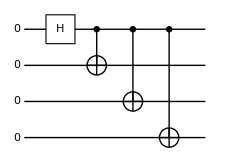

can generate a state of the form

GHZ:=(0⊗0⊗⋯⊗0+1⊗1⊗⋯⊗1)/(√2) .

The above state, which is known as the Greenberger-Horne-Zeilinger (GHZ) state (Greenberger et al., 1989), exhibits a quantum entanglement of more than two particles. It has stimulated tests of non-locality of quantum mechanics beyond Bell inequalities (Bouwmeester et al., 1999; Pan et al., 2000).

Quantum entanglement is a valuable resource in quantum information processing and in quantum communication. The most popular example of such is quantum teleportation.

In the above consideration, CNOT gates with the same control qubit are applied on different target qubits. The opposite setting brings forth additional applications of CNOT as illustrated in the following quantum circuit.

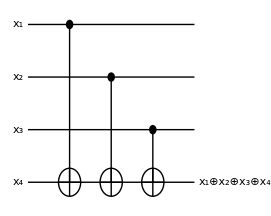

In this quantum circuit, the successive application of the CNOT gates on the same target qubit with different control qubits results in the accumulation of the logical bit values of all qubits. The same goal may be achieved by applying the CNOT gates on the consecutive pairs of qubits as

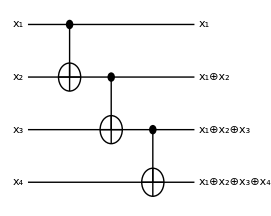

In this case, not only the last qubit but also the qubits in the middle are modified. However, this makes little difference since the quantum circuit block is mostly used to conditionally control the operation of an unitary gate on a different qubit and the whole block must be undone anyway (see, for example, the quantum circuit of conditional unitary gate).

Controlled-Z Gate (CZ)

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

An interesting variant of CNOT gates is the so-called controlled-Z or CZ gate. This is a quantum logic gate on two qubits that maps the logical basis states as

CZ:c⊗t↦c⊗(t(-1))^(c t)

for c,t∈{0,1}.

```mathematica
op=CZ[S[1],S[2]]
```

CZ[{S_1},{S_2}]

```mathematica
in=Basis[S@{1,2}];
out=op**in;
Thread[in->out]//LogicalForm//TableForm
```

0_S_10_S_2→0_S_10_S_2
0_S_11_S_2→0_S_11_S_2
1_S_10_S_2→1_S_10_S_2
1_S_11_S_2→-1_S_11_S_2

The matrix representation of the CZ gate in the logical basis is given by

```mathematica
Matrix[op]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)

Since it is symmetric for the two qubits, a distinction of the control and target qubit is meaningless. Accordingly, in quantum circuit model, the gate is depicted by the following quantum circuit element

```mathematica
QuantumCircuit[op]
```

-Graphics-

The filled circles on both qubit lines (rather than a square box on either qubit) indicate that the bit values of both qubits remain unchanged.

Noting the identity H Z H=X, one can regard that the CZ gate is equal to the CNOT gate up to the Hadamard gate on the target qubit. The relation between the CNOT and CZ gate is illustrated in the following quantum circuits

-Graphics-

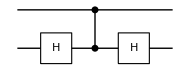

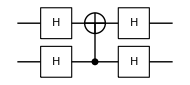

```mathematica
cnot=QuantumCircuit[CNOT[S[1],S[2]]]
cz1=QuantumCircuit[S[2,6],CZ[S[1],S[2]],S[2,6]]
cz2=QuantumCircuit[S[{1,2},6],CNOT[S[2],S[1]],S[{1,2},6]]
```

```mathematica
cnot==cz1==cz2//Elaborate
```

True

Depending on the Hamiltonian of a particular physical system, direct realization of the CNOT gate may be considerably difficult while the CZ gate is relatively easier to implement. In such a case, the above identity offers a straightforward workaround for a physical implementation of the CNOT gate.

SWAP Gate

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

Another interesting two-qubit gate is the SWAPpaclet:Q3/ref/SWAPQ3 Package Symbol gate that ‘swaps’ the states of the two qubits and maps the logical basis states as

SWAP:x_1⊗x_2↦x_2⊗x_1

for x_1,x_2∈{0,1}.

```mathematica
op=SWAP[S[1],S[2]];
in=Basis[S@{1,2}];
out=op**in;
Thread[in->out]//LogicalForm//TableForm
```

0_S_10_S_2→0_S_10_S_2
0_S_11_S_2→1_S_10_S_2
1_S_10_S_2→0_S_11_S_2
1_S_11_S_2→1_S_11_S_2

Given that the states 0⊗0 and 1⊗1 are not altered by the operation, the
matrix representation is given by

```mathematica
Matrix[op]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)

In quantum circuit model, it is depicted as

```mathematica
qc=QuantumCircuit[op]
```

-Graphics-

The SWAP gate can be implemented using the CNOT gate. To see this, first note that a simultaneous exchange of the second and fourth columns and rows of the above matrix leads to

```mathematica
CNOT[S[1],S[2]]//Matrix//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

which is nothing other than the matrix representation of the CNOT gate. On the other hand, the exchange of the second and fourth columns and rows is equivalent to flipping the bit values of the first qubit only when the second qubit is set to |1⟩. Hence, it corresponds to the CNOT gate with the second and first qubit as the control and target qubit, respectively. In short, the SWAP gate can be achieved by a combination of the CNOT gates as follows

-Graphics-

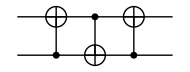

```mathematica
swap=QuantumCircuit[SWAP[S[1],S[2]]]
cnot=QuantumCircuit[CNOT[S[2],S[1]],CNOT[S[1],S[2]],CNOT[S[2],S[1]]]
```

```mathematica
swap==cnot//Elaborate
```

True

Interestingly, the SWAP gate itself is not universal, but the √SWAP gate—the gate that equals SWAP when squared—is universal. That is, any quantum gate on a multi-qubit system can be implemented by combining √SWAP and single-qubit rotations. Indeed, one can combine the √SWAP gate with single-qubit rotations to construct the CZ gate (see the demonstration below). As discussed above, the CZ gate requires just two more Hadamard gates to implement the CNOT gate, and it is hence universal.

Let us construct the CZ gate with the √SWAPgate. Here is the matrix representation of the the √SWAPgate.

```mathematica
mat=MatrixPower[Matrix@Elaborate@SWAP[S[1],S[2]],1/2];
mat//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1/2+ⅈ/2 | 1/2-ⅈ/2 | 0
0 | 1/2-ⅈ/2 | 1/2+ⅈ/2 | 0
0 | 0 | 0 | 1)

This is an explicit operator expression of the √SWAPgate in terms of the Pauli operators.

```mathematica
sqrtSWAP={ExpressionFor[mat,S@{1,2}],"Label"->"√U"}
```

{(3/4+ⅈ/4)+(1/4-ⅈ/4) S_1^z S_2^z+(1/2-ⅈ/2) S_1^+S_2^-+(1/2-ⅈ/2) S_1^-S_2^+,Label→√U}

This is a quantum circuit model to construct the CZ gate from the √SWAP gate and single-qubit rotation gates. In this diagram, √U denotes the √SWAPgate and S the quadrant phase gate (or, equivalently, the rotation around the z-axis by angle π/2).

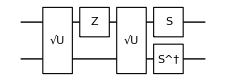

```mathematica
qc=QuantumCircuit[sqrtSWAP,S[1,3],sqrtSWAP,{S[1,7],Dagger@S[2,7]}]
```

To check if it indeed implements the CZ gate, take a look at the matrix representation of the quantum circuit model.

```mathematica
Matrix[qc]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)

Controlled-Unitary Gates

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

### Definition

Consider two qubits that are once again called control and target qubits. Let U be a unitary operator on the target qubit. The controlled-U gate is a unitary operator on the two-qubit Hilbert space defined, analogously to CNOT, by

Ctrl(U):c⊗t↦c⊗(U^c t).

or equivalently,

Ctrl(U):=00⊗I+11⊗U.

If the control qubit is in |0⟩, then it does nothing. On the other hand, if the control qubit is in |1⟩, then it operates unitary operator U on the target qubit.

Analogously to the CNOT gate, the matrix representation of the controlled-unitary gate is thus given by

Ctrl(U)≐(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | U_11 | U_12
0 | 0 | U_21 | U_22) .

where U_(i j) are the elements of the matrix representation of U.

In quantum circuit model, a controlled-unitary gate is depicted as

.

The filled circle connected to the quantum circuit element on the target qubit indicates the conditional operation of the element conditioned on the state of the control qubit.

For demonstration, consider a single-qubit rotation acting on the qubit S[2,None]. It is a rotation around the y-axis by angle ϕ.

```mathematica
Let[Real,ϕ]
U=Rotation[ϕ,S[2,2],"Label"->"U"];
U//Elaborate//Matrix//MatrixForm
```

(Cos[ϕ/2] | -Sin[ϕ/2]
Sin[ϕ/2] | Cos[ϕ/2])

This is a quantum circuit featuring the controlled-unitary gate.

```mathematica
qc=QuantumCircuit[ControlledU[S[1],U]]
```

-Graphics-

This is the explicit expression of the controlled-U gate  in terms of the Pauli operators.

```mathematica
Elaborate[qc]
```

Cos[ϕ/4]^2+S_1^z Sin[ϕ/4]^2+1/2 ⅈ S_1^z S_2^y Sin[ϕ/2]-1/2 ⅈ S_2^y Sin[ϕ/2]

The controlled-U gate maps the logical basis states as follows.

```mathematica
in=Basis[S@{1,2}];
out=qc**in;
Thread[in->out]//LogicalForm//TableForm
```

0_S_10_S_2→0_S_10_S_2
0_S_11_S_2→0_S_11_S_2
1_S_10_S_2→Cos[ϕ/2] 1_S_10_S_2+1_S_11_S_2 Sin[ϕ/2]
1_S_11_S_2→Cos[ϕ/2] 1_S_11_S_2-1_S_10_S_2 Sin[ϕ/2]

When the control qubit  is in a superposition, the resulting state is an entangled state in general.

```mathematica
in=Ket[]+Ket[S[1]->1];
LogicalForm[in,S@{1,2}]
```

0_S_10_S_2+1_S_10_S_2

```mathematica
out=qc**in;
LogicalForm[out,S@{1,2}]
```

0_S_10_S_2+Cos[ϕ/2] 1_S_10_S_2+1_S_11_S_2 Sin[ϕ/2]

### Phase Acquisition

An important aspect of a controlled-unitary operator is that it induces relative phase shifts on the control qubit when the target qubit has been prepared in an eigenstate of U. At first glace, it may sound counterintuitive since the definition given above seems to indicate that it changes only the target qubit depending on the state of the control qubit and keeps the latter intact. This is another feature distinguishing quantum gates from their classical counterparts.

Let us take a closer look to see how this works. Prepare the control qubit in a superposition ψ=0+1 and the target qubit in an eigenstate ϕ of U with eigenvalue ⅇ^(ⅈ ϕ). The controlled-unitary gate transforms the state to

ψ⊗ϕ→0⊗ϕ+1⊗(Uϕ)→0⊗ϕ+1⊗ϕ ⅇ^(ⅈ ϕ)→(0+1 ⅇ^(ⅈ ϕ))⊗ϕ .

This feature is extended to multi-control unitary gates and plays a crucial role in many quantum algorithms. In particular, the quantum phase estimation algorithm is a direct consequence of this feature.

For demonstration, consider the phase gate. Recall that state 1 is an eigenstate of it with eigenvalue ⅇ^(ⅈ ϕ).

```mathematica
U=Phase[ϕ,S[2]]
Matrix[U]//MatrixForm
```

Phase[ϕ,S_2]

(1 | 0
0 | ⅇ^(ⅈ ϕ))

We are interested in the following controlled-unitary gate.

```mathematica
op=ControlledU[S[1],U];
QuantumCircuit[op]
```

-Graphics-

Prepare the target qubit in the eigenstate with a finite phase shift. In addition, prepare the control qubit in a linear superposition of the computational basis states in order to pick up the phase shift.

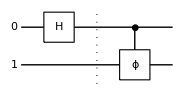

```mathematica
qc=QuantumCircuit[Ket[S[2]->1,S@{1,2}],
S[1,6],"Separator",op]
```

Observe that the state does not change on the target qubit while the phase shift induced by the phase gate has been picked up by the state in the control qubit.

```mathematica
out=Elaborate[qc];
out//KetFactor//LogicalForm
```

((0_S_1+ⅇ^(ⅈ ϕ) 1_S_1)⊗1_S_2)/(√2)

### Application: Conditional Operation

The CNOT gate and the controlled-unitary gate can be combined to achieve a variety of conditional gate operations. For example, consider a system consisting of a control register of n qubits and a target register of a single qubit. Suppose that you want to operate a unitary gate U on the target qubit only when an odd number of the control qubits is set to |1⟩,

c⊗t↦c⊗(U^(c_1⊕c_2⊕⋯⊕c_n)t) .

First, operate the CNOT gates consecutively with the first (n − 1) qubits in the control register as the control qubit and the last qubit in the control register as the target qubit. This transforms the n^th qubit toc_1⊕c_2⊕⋯⊕c_n. Then, the desired operation is implemented by applying the controlled-U gate controlled by the n^th qubit. To get the control qubits back to the original state, operate the CNOT gates in the reverse order. Overall, the following quantum circuit implements the conditional operation

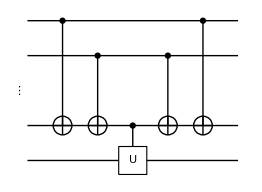
-Graphics-.

This method is used to implement a multi-control unitary gate based on the Gray code.

As a demonstration, consider a three-qubit control register. Suppose that we want to operate a rotation around the y-axis on the target qubit.

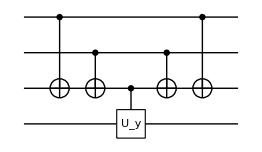

```mathematica
$n=3;
ss=S[Range[$n],None];
cnot=Distribute[CNOT[Most[ss],Last@ss],List];
U=Rotation[ϕ,S[$n+1,2]];
qc=QuantumCircuit[
Sequence@@cnot,
ControlledU[S[$n],U],
Sequence@@Reverse[cnot]
]
```

Note the way the logical basis states are transformed through the above quantum circuit.

```mathematica
in=Basis[ss];
out=qc**in;
Thread[in->out]//LogicalForm//TableForm
```

0_S_10_S_20_S_30_S_4→0_S_10_S_20_S_30_S_4
0_S_10_S_21_S_30_S_4→Cos[ϕ/2] 0_S_10_S_21_S_30_S_4+0_S_10_S_21_S_31_S_4 Sin[ϕ/2]
0_S_11_S_20_S_30_S_4→Cos[ϕ/2] 0_S_11_S_20_S_30_S_4+0_S_11_S_20_S_31_S_4 Sin[ϕ/2]
0_S_11_S_21_S_30_S_4→0_S_11_S_21_S_30_S_4
1_S_10_S_20_S_30_S_4→Cos[ϕ/2] 1_S_10_S_20_S_30_S_4+1_S_10_S_20_S_31_S_4 Sin[ϕ/2]
1_S_10_S_21_S_30_S_4→1_S_10_S_21_S_30_S_4
1_S_11_S_20_S_30_S_4→1_S_11_S_20_S_30_S_4
1_S_11_S_21_S_30_S_4→Cos[ϕ/2] 1_S_11_S_21_S_30_S_4+1_S_11_S_21_S_31_S_4 Sin[ϕ/2]

### Decomposition into Elementary Gates

How can you implement a controlled-unitary gate? The operation involves only two qubits, and in principle, it should be possible to implement any specific controlled-unitary gate. However, the requirements for a physical implementation of two-qubit gates is far more difficult to fulfill on realistic systems than for single-qubit gates. Fortunately, any controlled-unitary gate can be implemented using only the CNOT gate and single-qubit gates. This is one of the basic steps in establishing universal quantum computation.

Let U be a unitary gate on the second (target) qubit controlled by the first (control) qubit. Suppose that U has Euler angles α, β, and γ and an additional phase factor ⅇ^(ⅈ φ),

U=ⅇ^(ⅈ φ)U_z(α)U_y(β)U_z(γ) .

Then one can always find three unitary operators A, B, and C such that

U=ⅇ^(ⅈ φ)A X B X C ,	A B C=I ,

where X is the Pauli X operator. More explicitly, a common choice is

A=U_z(α)U_y(β/2) ,

B=U_y(-β/2)U_z(-(α+γ)/2) ,

C=U_z(-(α-γ)/2)U_y(β)U_z(γ) .

Since U_(y/z)(ϕ)=X U_(y/z)(-ϕ)X for any ϕ, the above choice satisfies the desired properties. These properties imply that the controlled-unitary gate can be implemented as in the following quantum circuit

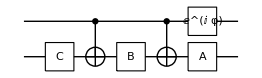
=-Graphics-

where the last gate on the first qubit is the relative phase shift by φ, 00+11 ⅇ^(ⅈ φ). Indeed, when the control qubit is in |0⟩, the two CNOT gates in the middle do nothing, and the combined operator A B C on the target qubit ends up with the identity operator. With the control qubit in |1⟩, on the other hand, the two CNOT gates are operational and the overall operator on the target qubit becomes A X B X C=ⅇ^(-ⅈ φ)U, where the phase factor is canceled by the opposite phase from the control qubit.

For demonstration, consider a unitary matrix to be applied conditionally on the target qubit.

```mathematica
mat=I*TheRotation[Pi/3,{1,1,0}]//FullSimplify;
mat//MatrixForm
```

((ⅈ √3)/2 | -1/2 (-1)^(3/4)
1/2 (-1)^(1/4) | (ⅈ √3)/2)

We want to implement the following controlled-unitary gate.

```mathematica
op=ExpressionFor[mat,S[2]];
qc=QuantumCircuit[ControlledU[S[1],op,"Label"->"U"]]
```

-Graphics-

First, find the Euler angles of the unitary operator and the global phase factor.

```mathematica
det=Det[mat];
phi=Arg[det]/2;
{a,b,c}=TheEulerAngles[mat/Sqrt[det]]
```

{-π/4,π/3,π/4}

From the Euler angles, choose the component operators.

```mathematica
opA=EulerRotation[{a,b/2,0},S[2],"Label"->"A"];
opB=EulerRotation[{0,-b/2,-(a+c)/2},S[2],"Label"->"B"];
opC=EulerRotation[{0,0,-(a-c)/2},S[2],"Label"->"C"];
opD=Phase[phi,S[1]];
```

Finally, construct the equivalent quantum circuit model.

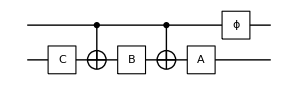

```mathematica
new=QuantumCircuit[opC,CNOT[S[1],S[2]],opB,CNOT[S[1],S[2]],opA,opD]
```

Check the result.

```mathematica
Elaborate[qc-new]//Chop
```

0

General Unitary Gates

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

Here we decompose an arbitrary two-qubit unitary gate into factors of controlled-unitary gates only. This is a remarkable advantage when one tries to build a quantum computer as you can just focus on how to implement the CNOT gate and single-qubit gates. Moreover, the same idea eventually leads to the proof of universal quantum computation on a larger system.

### Two-Level Unitary Transforms

Consider an arbitrary two-qubit unitary operator U. In the logical basis, it is represented by a unitary matrix

U=(U_11 | U_12 | U_13 | U_14
U_21 | U_22 | U_23 | U_24
U_31 | U_32 | U_33 | U_34
U_41 | U_42 | U_43 | U_44) .

To break the unitary operation U down into more elementary quantum logic gates, we make use of two-level unitary transformations. A two-level unitary transformation is a unitary operation with matrix representation that acts only on the two columns and rows of other matrices or column or row vectors. The descriptive word “two-level” should not be confused with “two-qubit”. A two-level transformation acts on multiple qubits, but it just transforms only two rows or columns at a time in the representation.

Let us start with a two-level unitary transformation of the form

T_1=(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | U_13^*/𝒩_1 | U_14/𝒩_1
0 | 0 | U_14^*/𝒩_1 | -U_13/𝒩_1)

with 𝒩_1:=√(|U_13|^2+|U_14|^2) such that T_1 T_1^†=T_1^†T_1=I. When it multiplies U from the right, it does not change the first two columns of U. It only alters the last two columns, and hence the name ‘two-level transformation’. The elements in the lower-right sub-block of T_1 have been chosen so that the first element of the last column is canceled:

U T_1=(U_11 | U_12 | U_13^′ | 0
U_21 | U_22 | U_23^′ | U_24^′
U_31 | U_32 | U_33^′ | U_34^′
U_41 | U_42 | U_43^′ | U_44^′) .

Now take another two-level unitary transformation, this time, of the form

T_2=(1 | 0 | 0 | 0
0 | U_12^*/𝒩_2 | U_13^′/𝒩_2 | 0
0 | U_13^(′*)/𝒩_2 | -U_12/𝒩_2 | 0
0 | 0 | 0 | 1) ,

where 𝒩_2 is a normalization factor like 𝒩_1 so that T_2 T_2^†=T_2^†T_2=I. It removes U_13^′ while keeping the first and last column as they are:

U T_1 T_2=(U_11 | U''_12 | 0 | 0
U_21 | U''_22 | U''_23 | U_24^′
U_31 | U''_32 | U''_33 | U_34^′
U_41 | U''_42 | U''_43 | U_44^′) .

Similarly, we go further with the two-level unitary matrix

T_3=(U_11^*/𝒩_3 | U''_12/𝒩_3 | 0 | 0
U_12^(″*)/𝒩_3 | -U_11/𝒩_3 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

to remove element U''_12 and get

U T_1 T_2 T_3=(U'''_11 | 0 | 0 | 0
0 | U'''_22 | U''_23 | U_24^′
0 | U'''_32 | U''_33 | U_34^′
0 | U'''_42 | U''_43 | U_44^′) .

At this stage, all elements except for the first of the first column vanish (U'''_21=U'''_31=U'''_41=0) the product U T_1 T_2 T_3 is a unitary matrix.

Repeating the procedure, we can remove all off-diagonal elements to get

U T_1 T_2⋯ T_L=I .

As Tj are all unitary, it enables us to rewrite U in a combination of two-level unitary transformations, that is,

U =T_L^†⋯ T_2^†T_1^† .

For demonstration, consider a Hermitian operator on a two-qubit system. Physically, it corresponds to a transverse-field Ising model.

```mathematica
H=S[1,1]**S[2,1]+S[1,2]+S[2,2]+S[1,3]+S[2,3]
Matrix[H]//MatrixForm
```

S_1^x S_2^x+S_1^y+S_1^z+S_2^y+S_2^z

(2 | -ⅈ | -ⅈ | 1
ⅈ | 0 | 1 | -ⅈ
ⅈ | 1 | 0 | -ⅈ
1 | ⅈ | ⅈ | -2)

This is the unitary operator generated by the above Hermitian operator.

```mathematica
U=MultiplyExp[-I  H Pi/4]
```

ⅇ^(-1/4 ⅈ π (S_1^x S_2^x+S_1^y+S_1^z+S_2^y+S_2^z))

This shows the matrix representation of U in the logical basis.

```mathematica
mat=Matrix[U]//Simplify;
mat//MatrixForm
```

(-(1/2+(5 ⅈ)/6)/(√2) | -(1/6-ⅈ/2)/(√2) | -(1/6-ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2)
(1/6-ⅈ/2)/(√2) | (1/2+ⅈ/6)/(√2) | -(1/2+(5 ⅈ)/6)/(√2) | -(1/2+ⅈ/2)/(√2)
(1/6-ⅈ/2)/(√2) | -(1/2+(5 ⅈ)/6)/(√2) | (1/2+ⅈ/6)/(√2) | -(1/2+ⅈ/2)/(√2)
(1/2-ⅈ/2)/(√2) | (1/2+ⅈ/2)/(√2) | (1/2+ⅈ/2)/(√2) | -(1/2-ⅈ/2)/(√2))

This shows the decomposition of the unitary matrix into two-level matrices (displaying the first three elements). For the purpose of efficiency, the resulting list is given in terms of TwoLevelU.

```mathematica
twl=TwoLevelDecomposition[mat]//Simplify;
twl[[;;3]]
```

{TwoLevelU[{{1,0},{0,1}},{3,4},4],TwoLevelU[{{(1/2-(3 ⅈ)/2)/(√7),-(3/2+(3 ⅈ)/2)/(√7)},{(3/2-(3 ⅈ)/2)/(√7),(1/2+(3 ⅈ)/2)/(√7)}},{3,4},4],TwoLevelU[{{-(1-3 ⅈ)/(√38),√(14/19)},{-√(14/19),-(1+3 ⅈ)/(√38)}},{2,3},4]}

For a more intuitive form, you can convert TwoLevelU into the normal matrix form using Matrix. Here the first three are shown.

```mathematica
MatrixForm/@Matrix/@twl[[;;3]]
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | (1/2-(3 ⅈ)/2)/(√7) | -(3/2+(3 ⅈ)/2)/(√7)
0 | 0 | (3/2-(3 ⅈ)/2)/(√7) | (1/2+(3 ⅈ)/2)/(√7)),(1 | 0 | 0 | 0
0 | -(1-3 ⅈ)/(√38) | √(14/19) | 0
0 | -√(14/19) | -(1+3 ⅈ)/(√38) | 0
0 | 0 | 0 | 1)}

Indeed, they reconstruct the original matrix.

```mathematica
new=Dot@@Matrix/@twl;
mat-new//Simplify//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

### Two-Level Unitary Transformations with Controlled-Unitary Gates

We are still to express the two-level unitary transformations in terms of controlled-unitary gates. The two-level unitary matrix of the form

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | U_11 | U_12
0 | 0 | U_21 | U_22)

is already in the form of the matrix representation of a controlled-unitary gate, and just corresponds to a single controlled-unitary

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | U_11 | U_12
0 | 0 | U_21 | U_22)  = .

A two-level unitary matrix of the form

(1 | 0 | 0 | 0
0 | U_11 | 0 | U_12
0 | 0 | 1 | 0
0 | U_21 | 0 | U_22)

also corresponds to a single controlled-unitary gate with the control and target qubit exchanged. Here, the first qubit is the target qubit and the second the control qubit:

(1 | 0 | 0 | 0
0 | U_11 | 0 | U_12
0 | 0 | 1 | 0
0 | U_21 | 0 | U_22)  = .

More complicated is the two-level unitary matrix of the form

(1 | 0 | 0 | 0
0 | U_11 | U_12 | 0
0 | U_21 | U_22 | 0
0 | 0 | 0 | 1) .

As it affects both qubits, it cannot be represented by a single controlled-unitary gate. However, it is possible to bring it to the second of the above two forms by simultaneously exchanging the last two columns and rows.

(1 | 0 | 0 | 0
0 | U_11 | U_12 | 0
0 | U_21 | U_22 | 0
0 | 0 | 0 | 1)→(1 | 0 | 0 | 0
0 | U_11 | 0 | U_12
0 | 0 | 1 | 0
0 | U_21 | 0 | U_22) .

The specified exchanges correspond to flipping the bit values of the second qubit only when the first qubit has a value of 1, and they can be implemented by applying the CNOT gate with the first qubit as the control qubit and the second qubit as the target qubit. These observations lead to the following equivalence,

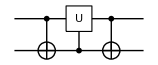
(1 | 0 | 0 | 0
0 | U_11 | U_12 | 0
0 | U_21 | U_22 | 0
0 | 0 | 0 | 1) = -Graphics-.

which allows us to implement the two-level unitary transformation with two CNOT gates and a controlled-unitary gate.

Of course, the way is not unique. For example, it is also possible to bring the same two-level unitary matrix to the first two-level unitary form, this time, by simultaneously exchanging the second and fourth columns and rows.

(1 | 0 | 0 | 0
0 | U_11 | U_12 | 0
0 | U_21 | U_22 | 0
0 | 0 | 0 | 1)→(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | U_22 | U_21
0 | 0 | U_12 | U_11) .

These exchanges correspond to flipping the bit values of the first qubit only when the second qubit has a value of 1, that is, to applying the CNOT gate with the second qubit as the control qubit and the first qubit as the target qubit. Note that in this case, unitary matrix U itself is modified through the exchanges, and the rows and columns of U are exchanged. This is equivalent to the basis change by the Pauli X matrix, U → U ' = X U X. Putting all together, the two-level unitary matrix is implemented as

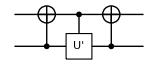
(1 | 0 | 0 | 0
0 | U_11 | U_12 | 0
0 | U_21 | U_22 | 0
0 | 0 | 0 | 1) = -Graphics-.

In a similar manner, we can implement another form of two-level unitary matrix as

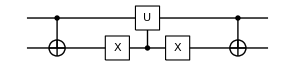
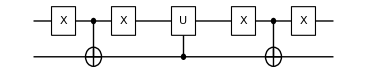
(U_11 | 0 | 0 | U_12
0 | 1 | 0 | 0
0 | 0 | 1 | 0
U_21 | 0 | 0 | U_22)  = -Graphics-= -Graphics-.

For a demonstration, consider a single-qubit rotation around the y-axis.

```mathematica
U=Rotation[ϕ,S[1,2],"Label"->"U"];
Matrix[U]//MatrixForm
```

(Cos[ϕ/2] | -Sin[ϕ/2]
Sin[ϕ/2] | Cos[ϕ/2])

This is the two-level unitary transformation to be implemented with elementary gates.

```mathematica
op=TwoLevelU[Matrix[U],{1,4},4];
Matrix[op]//MatrixForm
```

(Cos[ϕ/2] | 0 | 0 | -Sin[ϕ/2]
0 | 1 | 0 | 0
0 | 0 | 1 | 0
Sin[ϕ/2] | 0 | 0 | Cos[ϕ/2])

This quantum circuit shows one implementation.

```mathematica
qc1=QuantumCircuit[
CNOT[S[1],S[2]],"Spacer",
S[2,1],ControlledU[S[2],U],S[2,1],
"Spacer",CNOT[S[1],S[2]],
"PortSize"->0.1]
```

-Graphics-

This is another implementation.

```mathematica
qc2=QuantumCircuit[
S[1,1],CNOT[S[1],S[2]],S[1,1],"Spacer",
ControlledU[S[2],U],
"Spacer",S[1,1],CNOT[S[1],S[2]],S[1,1],
"PortSize"->0.1]
```

-Graphics-

Check the equivalence of the two-level unitary matrix and the implementations

```mathematica
Matrix[op]-Matrix[qc1]//Normal//Simplify//MatrixForm
Matrix[op]-Matrix[qc2]//Normal//Simplify//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

So far, we have determined the implementations of 4 × 4 two-level unitary matrices of different forms just by inspection, that is, in an ad hoc manner. For more than two qubits, the size of the two-level unitary matrices is much larger, and it is difficult to find proper implementations in such a way. Fortunately, there is a systematic way based on the Gray code.

### Demonstration

In the above, we have shown that an arbitrary two-qubit unitary gate can be carried out by first decomposing its matrix representation into two-level unitary matrices and then implementing the two-level unitary matrices by means of the CNOT and controlled-unitary gates. Here we demonstrate the whole procedure.

Consider a two-qubit model. Physically, it describes two qubits coupled with each other through an Ising-type couping and subject to an external magnetic field..

```mathematica
H=S[1,1]**S[2,1]+S[1,2]+S[2,2]+S[1,3]+S[2,3]
```

S_1^x S_2^x+S_1^y+S_1^z+S_2^y+S_2^z

We are interested in simulating the time-evolution operator governed by the above Hamiltonian.

```mathematica
U=MultiplyExp[-I  H*Pi/4]
```

ⅇ^(-1/4 ⅈ π (S_1^x S_2^x+S_1^y+S_1^z+S_2^y+S_2^z))

This is the 4×4 unitary matrix to implement in terms of elementary gates.

```mathematica
mat=Matrix[U,S@{1,2}];
mat//MatrixForm
```

(-(1/2+(5 ⅈ)/6)/(√2) | -(1/6-ⅈ/2)/(√2) | -(1/6-ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2)
(1/6-ⅈ/2)/(√2) | (1/2+ⅈ/6)/(√2) | -(1/2+(5 ⅈ)/6)/(√2) | -(1/2+ⅈ/2)/(√2)
(1/6-ⅈ/2)/(√2) | -(1/2+(5 ⅈ)/6)/(√2) | (1/2+ⅈ/6)/(√2) | -(1/2+ⅈ/2)/(√2)
(1/2-ⅈ/2)/(√2) | (1/2+ⅈ/2)/(√2) | (1/2+ⅈ/2)/(√2) | -(1/2-ⅈ/2)/(√2))

First, decompose the 4×4 unitary matrix into the two-level unitary matrices.

```mathematica
twl=TwoLevelDecomposition[mat]//Simplify;
MatrixForm/@Matrix/@twl
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | (1/2-(3 ⅈ)/2)/(√7) | -(3/2+(3 ⅈ)/2)/(√7)
0 | 0 | (3/2-(3 ⅈ)/2)/(√7) | (1/2+(3 ⅈ)/2)/(√7)),(1 | 0 | 0 | 0
0 | -(1-3 ⅈ)/(√38) | √(14/19) | 0
0 | -√(14/19) | -(1+3 ⅈ)/(√38) | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -(5/14+(5 ⅈ)/14)/(√2) | (3 √19)/14
0 | 0 | -(3 √19)/14 | -(5/14-(5 ⅈ)/14)/(√2)),(-(1/2+(5 ⅈ)/6)/(√2) | (√19)/6 | 0 | 0
-(√19)/6 | -(1/2-(5 ⅈ)/6)/(√2) | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | -(1-3 ⅈ)/(√38) | √(14/19) | 0
0 | -√(14/19) | -(1+3 ⅈ)/(√38) | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -(1/2-(3 ⅈ)/2)/(√7) | (3/2-(3 ⅈ)/2)/(√7)
0 | 0 | -(3/2+(3 ⅈ)/2)/(√7) | -(1/2+(3 ⅈ)/2)/(√7))}

Next, rewrite the two-level unitary matrices in terms of the CNOT and controlled-unitary gates. The first element of list twl happens to be the identity matrix in this case, and it is excluded in the further analysis.

```mathematica
gates=GrayTwoLevelU[#,S@{1,2}]&/@Rest[twl]
```

{{ControlledU[{S_1},1/(2 √7)-(3 ⅈ S_2^x)/(2 √7)-(3 ⅈ S_2^y)/(2 √7)-(3 ⅈ S_2^z)/(2 √7),Label→U]},{CNOT[{S_2},{S_1}],ControlledU[{S_1},-1/(√38)-ⅈ √(14/19) S_2^y-(3 ⅈ S_2^z)/(√38),Label→U],CNOT[{S_2},{S_1}]},{ControlledU[{S_1},-5/(14 √2)+3/14 ⅈ √19 S_2^y-(5 ⅈ S_2^z)/(14 √2),Label→U]},{{S_1^x},ControlledU[{S_1},-1/(2 √2)+1/6 ⅈ √19 S_2^y-(5 ⅈ S_2^z)/(6 √2),Label→U],{S_1^x}},{CNOT[{S_2},{S_1}],ControlledU[{S_1},-1/(√38)-ⅈ √(14/19) S_2^y-(3 ⅈ S_2^z)/(√38),Label→U],CNOT[{S_2},{S_1}]},{ControlledU[{S_1},-1/(2 √7)-(3 ⅈ S_2^x)/(2 √7)+(3 ⅈ S_2^y)/(2 √7)+(3 ⅈ S_2^z)/(2 √7),Label→U]}}

This shows the overall quantum circuit model. Here the same label “U” has been used for different controlled-unitary gates just for convenience. Do not forget to reverse the order before plugging the gates in the quantum circuit model.

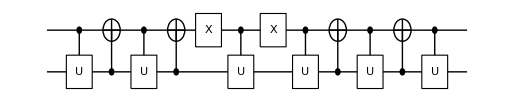

```mathematica
qc=QuantumCircuit@@Reverse@Flatten[gates]
```

Check the above quantum circuit by converting it into the matrix representation.

```mathematica
new=Matrix[qc]//Normal//Simplify;
new//MatrixForm
```

(-(1/2+(5 ⅈ)/6)/(√2) | -(1/6-ⅈ/2)/(√2) | -(1/6-ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2)
(1/6-ⅈ/2)/(√2) | (1/2+ⅈ/6)/(√2) | -(1/2+(5 ⅈ)/6)/(√2) | -(1/2+ⅈ/2)/(√2)
(1/6-ⅈ/2)/(√2) | -(1/2+(5 ⅈ)/6)/(√2) | (1/2+ⅈ/6)/(√2) | -(1/2+ⅈ/2)/(√2)
(1/2-ⅈ/2)/(√2) | (1/2+ⅈ/2)/(√2) | (1/2+ⅈ/2)/(√2) | -(1/2-ⅈ/2)/(√2))

```mathematica
new-mat//Simplify//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

| Related Guides
▪Quantum Computation and Quantum Information

| Related Tutorials
▪Quantum Computation: Overview
▪Quantum Computation and Quantum Information with Q3

| Related Links
▪D. M. Greenberger, M. A. Horne, & A. Zeilinger, “Going beyond Bell’s theorem,”http://arxiv.org/abs/0712.0921 in Bell’s Theorem, Quantum Theory, and Conceptions of the Universe, edited by Kafatos, M. (Kluwer Academic, Dordrecht, The Netherlands, 1989).
▪D. Bouwmeester, J.-W. Pan, M. Daniell, H. Weinfurter, & A. Zeilinger, Phys. Rev. Lett. 82 (7), 1345 (1999)https://doi.org/10.1103/PhysRevLett.82.1345, “Observation of Three-Photon Greenberger- Horne-Zeilinger Entanglement.”
▪J.-W. Pan, D. Bouwmeester, M. Daniell, H. Weinfurter, & A. Zeilinger, Nature 403, 515 (2000)https://doi.org/10.1038/35000514, “Experimental test of quantum nonlocality in three-photon Greenberger-Horne-Zeilinger entanglement.”
▪M. Nielsen and I. L. Chuang (2022)https://doi.org/10.1017/CBO9780511976667, Quantum Computation and Quantum Information (Cambridge University Press, 2011).
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer, 2022).